William M. Kirby & Frederick W. Strauch
Williams College, Williamstown, MA, USA 01267
wmkirby1@gmail.com

Algorithm for efficient compilation of the Schur transform on n qubits into a product of two-level gates.

lop[d] returns the lowering operator J_-=J_(1-)+J_(2-) that acts on a composite system comprising a subsystem with total spin j_1 (corresponding to d dimensions), and a subsystem with total spin j_2=1/2 (corresponding to 2 dimensions).  Note: output vectors will not be normalized.

```mathematica
lop[d_]:=Module[{j1,m1,evec=Table[0,{i,1,d}],lop1={},lop2},
(* Get effective total spin for d-dimensional system. *)
j1=(d-1)/2;
(* First row of lowering operator is all zeros. *)
AppendTo[lop1,evec];
(* Get remaining rows of lowering operator for dimension d (total spin j1). *)
Do[
(* Get effective spin projection for index i in d-dimensions (total spin j1). *)
m1=j1+1-i;
AppendTo[lop1,ReplacePart[evec,i->Sqrt[j1(j1+1)-m1(m1-1)]]];,
{i,1,d-1}
];
(* Spin-1/2 lowering operator. *)
lop2={{0,0},{1,0}};
Return[KroneckerProduct[lop1,IdentityMatrix[2]]+KroneckerProduct[IdentityMatrix[d],lop2]]
];
```

CG[d] returns the Clebsch-Gordan transform that adds 1 new qubit to a d-dimensional pre-symmetrized system (that is, the basis vectors for the d-dimensional system have definite values of m2, the total spin projection for the system).
Input to matrix is a vector in product basis form: indices correspond to |m1,m2⟩, ordered by m1, then m2.
Output from matrix is a vector in standard symmetrized form: indices correspond to |j,m⟩, ordered by j, then m.

```mathematica
CG[d_]:=
Module[{j1,evec=Table[0,{i,1,2d}],cvec,mat={},lopd,a,b},
If[d==1,
mat={{1,0},{0,1}};,
(* Effective total spin of qubit is j2=1/2. Get effective total spin for d-dimensional system. *)
j1=(d-1)/2;
(* New total dimension is 2d. evec is an empty vector of dimension 2d. *)
(* Get first output basis vector with spin j1+1/2:
|j=j1+1/2,m=j1+1/2⟩ = |m1=j1,m2=1/2⟩ *)
cvec=ReplacePart[evec,1->1];
AppendTo[mat,cvec];
(* Lowering operator. *)
lopd=lop[d];
(* Get remaining output basis vectors with spin j1+1/2. *)
Do[
cvec=FullSimplify[(lopd.cvec)/Norm[lopd.cvec]];
AppendTo[mat,cvec];,
{i,1,d}
];
(* Get first output basis vector with spin j1-1/2:
must be a linear combination of |m1=j1,m2=-1/2⟩ and |m1=j1-1,m2=1/2⟩ that is orthogonal to the second output basis vector with spin j1+1/2 *)
cvec=ReplacePart[evec,{2->mat[[2,3]],3->-mat[[2,2]]}];
AppendTo[mat,cvec];
(* Get remaining output basis vectors with spin j1-1/2. *)
Do[
cvec=FullSimplify[(lopd.cvec)/Norm[lopd.cvec]];
AppendTo[mat,cvec];,
{i,1,d-2}
];
];
Return[mat]
];
```

Encode the information necessary to build a Schur transform out of successive Clebsch-Gordan transforms as follows:

A set of qubits called seq that encodes the set of standard tableaux whose shapes are order-2 partitions of n (the number of qubits). For each partition p, seq keeps track of the multiplicity of the irrep associated to p by labeling the copies of it by standard tableaux.

A set of qubits called par that encodes the set of order-2 partitions of n. These partitions label the irreps of the globally-symmetric unitary group on n qubits.

A set of qubits called stat that encodes the specific states within each irrep. The number of states in the irrep associated to partition p is given by the number of semistandard tableaux with shape p and entries in {1,2}.

CGBlocks[n,nstat] returns the generalized Clebsch-Gordan transform (in block diagonal form) associated to the addition of 1 new qubit to n already-symmetrized qubits.  nstat is the number of qubits used to encode stat.

Assumes input vector is in the form
(symmetrized vector for n qubits)⊗(new computational qubit)

Output vector is in symmetrized form (before reordering).

```mathematica
CGBlocks[n_,nstat_]:=
Module[{pars=Table[{n-p2,p2},{p2,0,Floor[n/2]}],npar,dstat,out,start,cg},
(* Get dimensions of stat for each irrep (labeled by partitions): *)
dstat=Table[p[[1]]-p[[2]]+1,{p,pars}];
If[n==1,npar=nstat-2,npar=nstat-1];
(* Initialize out: *)
out=SparseArray[Table[{i,i}->1,{i,1,2^(npar+nstat+1)}]];
Do[(* Iterate over distinct irreps: *)
(* Upper left corner location: *)
start=i 2^(nstat+1);
(* Get simple CG transform to be inserted: *)
cg=SparseArray[CG[dstat[[i+1]]]];
Do[
out[[start+k,start+l]]=cg[[k,l]];,
{k,1,2dstat[[i+1]]},
{l,1,2dstat[[i+1]]}
];,
{i,0,Length[pars]-1}
];
Return[out];
];
```

CGRearrange[] returns the permutation matrix that reorders the output of a CGBlocks[] transform by the new irreps (for n+1 qubits).  nstat is the number of qubits used to encode stat.

Assumes input vector is the output of the associated CGBlocks[] transform.

Output is in the form {matrix, locations}.  locations is a list whose elements have the form {inputlocation, outputlocation, dimension} with one element per output irrep: inputlocation indicates the location index of the input irrep corresponding to that output irrep, outputlocation indicates the location index of the output irrep, and dimension indicates the dimension of the output irrep.

```mathematica
CGRearrange[n_,nstat_]:=
Module[{pars=Table[{n-p2,p2},{p2,0,Floor[n/2]}],npar,dstat,xstart,ystart,m=Table[0,{i,0,Floor[(n+1)/2]+1}],swaps={},missingx={},missingy={},locations={}},
(* Get dimensions of stat for each irrep (labeled by partitions): *)
dstat=Table[p[[1]]-p[[2]]+1,{p,pars}];
If[n==1,npar=nstat-2,npar=nstat-1];
Do[(* Iterate over distinct irreps for n: *)
(* Move the first output irrep appearing in simple CG with input irrep pars[[i+1]]: *)
(* Start location for block (x coordinate): *)
xstart=i 2^(nstat+1);
(* Start location for block (y coordinate): *)
ystart=m[[i+1]]2^(npar+nstat)+i 2^(nstat);
(* m is a list that contains the numbers of each output irrep that have been moved to their correct locations so far: about to move top output irrep from input pars[[i+1]], so increment at [[i+1]]: *)
m[[i+1]]=m[[i+1]]+1;
(* Add permutation entries to swaps list: *)
Do[
AppendTo[swaps,{ystart+k,xstart+k}],
{k,1,dstat[[i+1]]+1}
];
(* Append upper-left corner location and dimension of block to locations: *)
AppendTo[locations,{i 2^(nstat+1),ystart,dstat[[i+1]]+1}];
(* Move the second output irrep appearing in simple CG with input irrep pars[[i+1]]: *)
xstart=i 2^(nstat+1)+dstat[[i+1]]+1;
ystart=m[[i+2]]2^(npar+nstat)+(i+1) 2^(nstat);
(* About to move bottom output irrep from input pars[[i+1]], so increment m at [[i+2]]: *)
m[[i+2]]=m[[i+2]]+1;
(* Add permutation entries to swaps list: *)
Do[
AppendTo[swaps,{ystart+k,xstart+k}],
{k,1,dstat[[i+1]]-1}
];
(* Append upper-left corner location and dimension of block to locations: *)
AppendTo[locations,{i 2^(nstat+1),ystart,dstat[[i+1]]-1}];,
{i,0,Length[pars]-1}
];
(* Fill in possible diagonal elements: *)
Do[
If[!(MemberQ[Flatten[swaps],i]),
AppendTo[swaps,{i,i}];
];,
{i,1,2^(npar+nstat+1)}
];
(* Reorder remaining indices to unused locations: *)
Do[
If[!MemberQ[Table[swaps[[j,1]],{j,1,Length[swaps]}],i],
AppendTo[missingx,i];
];,
{i,1,2^(npar+nstat+1)}
];
Do[
If[!MemberQ[Table[swaps[[j,2]],{j,1,Length[swaps]}],i],
AppendTo[missingy,i];
];,
{i,1,2^(npar+nstat+1)}
];
Do[
AppendTo[swaps,{missingx[[i]],missingy[[i]]}],
{i,1,Length[missingx]}
];
Return[{SparseArray[Table[swaps[[j]]->1,{j,1,Length[swaps]}]],locations}];
];
```

SchurDecompPartial[n] returns the decomposition of the Schur transform on n qubits into a sequence of super-CG transforms. Output is a list whose elements have form {top, matrix, bottom}, where top gives the number of qubits to be tensored in above (before) matrix, and bottom gives the number of qubits to be tensored in below (after).

```mathematica
SchurDecompPartial[n_]:=
Module[{nstat,out},
nstat=Floor[Log[2,n]]+1;
(* List of matrices whose product is the Schur transform: elements of list have form {top, matrix, bottom},where top is the number of qubits to be tensored in above (before) matrix, and bottom is the number of qubits to be tensored in below (after). *)
out=Table[{Max[0,n-2-i],CGRearrange[n-i,nstat][[1]].CGBlocks[n-i,nstat],i-1},{i,1,n-1}];
(*AppendTo[out,{0,CGRearrange[1,nstat][[1]].CGBlocks[1,nstat,True],n-2}];*)
Return[out];
];
```

SchurMatrix[n] returns the Schur transform matrix for n qubits. For the Schur transform matrix itself, the input register should be in the form

(seq qubits (ancillas))⊗(par qubits (ancillas))⊗(stat qubits (computational input))

The output register will have the same form.

```mathematica
SchurMatrix[n_]:=
Module[{list},
list=SchurDecompPartial[n];
Return[Apply[Dot,Table[KroneckerProduct[IdentityMatrix[2^list[[i]][[1]]],list[[i]][[2]],IdentityMatrix[2^list[[i]][[3]]]],{i,1,n-1}]]//FullSimplify]
];
```

Givens[mat] returns the direct decomposition of unitary u into a sequence of two-level (Givens) rotations. Output is a list of two-level rotations and one-level phases whose product is equal to u.

```mathematica
Givens[u_]:=
Module[{list={},v,d,b,c,g,ph},
d=Length[u];(* Dimension of goal unitary. *)
v=u//N;(* Stores current goal matrix. *)
Do[
Do[
If[v[[i,j]]≠0,
(* Build two-level rotation {{b,-c},{c,b}}, to zero v[[i,j]]. *)
b=v[[j,j]]/Sqrt[Abs[v[[i,j]]]^2+Abs[v[[j,j]]]^2];
c=-v[[i,j]]/Sqrt[Abs[v[[i,j]]]^2+Abs[v[[j,j]]]^2];
(* Insert two-level rotation into identity of dimension d. *)
g=IdentityMatrix[d];
g[[j,j]]=b;
g[[i,j]]=c;
g[[j,i]]=-c;
g[[i,i]]=b;
(* Add conjugate-transpose of Givens rotation to output list, and update v. *)
AppendTo[list,g†];
v=g.v//Chop;
];,
{j,1,i-1}
];,
{i,2,d}
];
(* Correct phases of diagonal elements. *)
Do[
If[v[[i,i]]!=1,
g=IdentityMatrix[d];
g[[i,i]]=v[[i,i]]*;
AppendTo[list,g†];
];,
{i,1,d}
];
Return[list]
];
```

**** MAIN PROCEDURE ****
SchurDecomp[n] returns the decomposition of the Schur transform on n qubits into a sequence of two-level rotations. Returns a list of elements with form {top, rotation, bottom}, where rotation is some two-level rotation, top is a number of qubits to be tensored in before the rotation, and bottom is a number of qubits to be tensored in after the rotation. That is, the Schur transform on n qubits is given by the product ∏_i M_i,  where M_i=𝕀_(2^top_i)⊗rotation_i⊗𝕀_(2^bottom_i).

```mathematica
SchurDecomp[n_]:=
Module[{list,givens,out={}},
list=SchurDecompPartial[n];
Do[
givens=Givens[cg[[2]]];
Do[
AppendTo[out,{cg[[1]],g,cg[[3]]}],
{g,givens}
];,
{cg,list}
];
Return[out]
];
```

SchurIndicesList[n] returns the a list of the rows used to encode the computational states in the Schur transform matrix (as output by SchurMatrix[n], or the product of the matrices output by SchurDecomp[n]).

```mathematica
SchurIndicesList[n_]:=
Module[{nstat,indiceslist,inputs,outputs={}},
nstat=Floor[Log[2,n]]+1;
indiceslist=Table[{Max[i-2,0],CGRearrange[i,nstat][[2]],n-1-i},{i,1,n-1}];
(* At this point, indiceslist has one element per super-CG transform in the decomposition of the Schur transform. Each of these elements is itself a list of form {top, irrepslist, bottom}, and irrepslist is a list whose elements have form {inputlocation, outputlocation, dimension}, as described above in the description of CGRearrange[]. *)

Do[
indiceslist[[i]]={indiceslist[[i]][[1]],(2^indiceslist[[i]][[3]])indiceslist[[i]][[2]]};,
{i,1,Length[indiceslist]}
];
(* At this point, indiceslist has one element per super-CG transform in the decomposition of the Schur transform. Each of these elements is itself a list, whose elements have form {top, {x, y, dimension}}, where x is the column corresponding to an input irrep, y is the row corresponding to an output irrep that comes from that input irrep, and dimension is the dimension of that output irrep. This list contains one element for each distinct output irrep. *)
Do[
indiceslist[[i]]=
Flatten[
Table[
Table[{l[[1]]+j(2^(n+2nstat-1-i)),l[[2]]+j(2^(n+2nstat-1-i)),l[[3]]},{l,indiceslist[[i]][[2]]}],
{j,0,-1+2^indiceslist[[i]][[1]]}],
1];,
{i,1,Length[indiceslist]}
];
(* At this point, indiceslist has one element per super-CG transform in the decomposition of the Schur transform. Each of these elements is itself a list, whose elements have form {x, y, dimension}, where x is the column corresponding to an input irrep, y is the row corresponding to an output irrep that comes from that input irrep, and dimension is the dimension of that output irrep. This list contains one element for each output irrep (from the previous step, we have added the multiplicities of the irreps). *)
Do[(* Start from the list corresponding to the super-CG transform that takes 2 qubits to 3 qubits and iterate to the list corresponding to the super-CG transform that takes n-1 qubits to n qubits... *)
inputs=Table[indiceslist[[i-1]][[j]][[2]],{j,1,Length[indiceslist[[i-1]]]}];
outputs={};
(* For each element in the current super-CG list, check whether its input corresponds to an output from the previous iteration. If it does, append it to the outputs list for this iteration. *)
Do[
If[MemberQ[inputs,slot[[1]]],
AppendTo[outputs,slot];
];,
{slot,indiceslist[[i]]}
];
(* Update indiceslist with the new (reduced) outputs list for this iteration. *)
indiceslist[[i]]=outputs;,
{i,2,Length[indiceslist]}
];
(* For the final output irrep indices, we only care about the outputs from the super-CG transform that takes n-1 qubits to n qubits. This corresponds to the last element in indiceslist, so we drop the others. Also, we no longer care about the input locations that led to these irreps, so drop those. *)
indiceslist=Table[indiceslist[[-1]][[i]][[2;;3]],{i,1,Length[indiceslist[[-1]]]}];
(* At this point, indiceslist has one element per output irrep of the Schur transform: elements have form {outputlocation, dimension}, where outputlocation is the location index of the irrep and dimension is its dimension.  For our final indiceslist, we want the rows corresponding to every state in every output irrep, not just the start locations for each irrep. *)
indiceslist=Flatten[
Table[Table[l[[1]]+j,{j,1,l[[2]]}],{l,indiceslist}],
1
];
(* Now indiceslist is in its final form: it is a list of the indices of every row corresponding to a state in an output irrep of the Schur transform. *)
Return[indiceslist]
];
```

SchurIndices[n] returns an association encoding the rows that contain the computational states in the Schur transform matrix (as output by SchurMatrix[n], or the product of the matrices output by SchurDecomp[n]). The output is an association such that the key {spin, k, m_s} maps to the row used to encode the state with spin projection m_s in the kth copy of the subspace with total spin spin. For example,

map = SchurIndices[3];
map[{3/2,1,1/2}]

returns 2, the output index of the state with spin projection 1/2 in the 1st copy of the spin-3/2 subspace.

```mathematica
SchurIndices[n_]:=
Module[{list,mults=Table[1,{i,1,Floor[n/2]+1}],init=1,dim=1,spin,multindex,out={}},
list=SchurIndicesList[n];
While[init≤Length[list],
While[(init+dim≤Length[list])&&(dim≤n)&&(list[[init+dim]]==list[[init+dim-1]]+1),
dim++;
];
spin=(dim-1)/2;
multindex=1+(n-dim+1)/2;
Do[
AppendTo[out,{spin,mults[[multindex]],spin-i}->list[[init+i]]],
{i,0,dim-1}
];
init=init+dim;
mults[[multindex]]=mults[[multindex]]+1;
dim=1;
];
Return[KeySortBy[Association[out],{Minus[#[[1]]]&,#[[2]]&,Minus[#[[3]]]&}]]
]
```

```mathematica
TextString[SchurIndices[4],AssociationFormat->{"{\n\t",",\n\t","\n}"," → "}]
```

{
	{2, 1, 2} → 1,
	{2, 1, 1} → 2,
	{2, 1, 0} → 3,
	{2, 1, -1} → 4,
	{2, 1, -2} → 5,
	{1, 1, 1} → 9,
	{1, 1, 0} → 10,
	{1, 1, -1} → 11,
	{1, 2, 1} → 41,
	{1, 2, 0} → 42,
	{1, 2, -1} → 43,
	{1, 3, 1} → 105,
	{1, 3, 0} → 106,
	{1, 3, -1} → 107,
	{0, 1, 0} → 17,
	{0, 2, 0} → 81
}

The figure below is a schematic for the complete Schur transform matrix for n qubits. Nonzero entries are dark, and active output rows are highlighted in red.

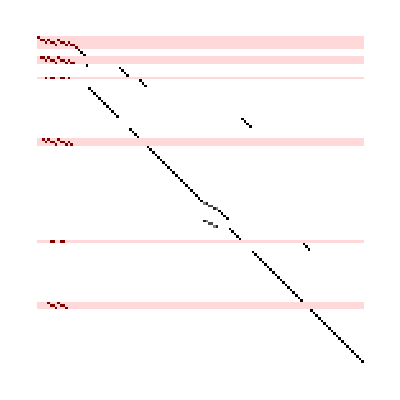

```mathematica
n=4;
mat=SchurMatrix[n];
rows=Table[0,{i,1,Length[mat]},{j,1,Length[mat]}];
vals=Values[SchurIndices[n]];
Do[
rows[[j,i]]=LightRed;,
{i,1,Length[mat]},
{j,vals}
];
ArrayPlot[mat+rows]
```

RestrictSchur[n] returns the Schur transform on n qubits, only including the computational input and output rows.

```mathematica
RestrictSchur[n_]:=
Module[{schur},
schur=SchurMatrix[n];
Table[schur[[i]][[1;;2^n]],{i,SchurIndices[n]}]
];
```

```mathematica
RestrictSchur[2]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1/(√2) | 1/(√2) | 0
0 | 0 | 0 | 1
0 | 1/(√2) | -1/(√2) | 0)

```mathematica
RestrictSchur[3]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√3) | 1/(√3) | 0 | 1/(√3) | 0 | 0 | 0
0 | 0 | 0 | 1/(√3) | 0 | 1/(√3) | 1/(√3) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | √(2/3) | -1/(√6) | 0 | -1/(√6) | 0 | 0 | 0
0 | 0 | 0 | 1/(√6) | 0 | 1/(√6) | -√(2/3) | 0
0 | 0 | 1/(√2) | 0 | -1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 1/(√2) | 0 | -1/(√2) | 0 | 0)